```mathematica
ClearAll["Global`*"]
```

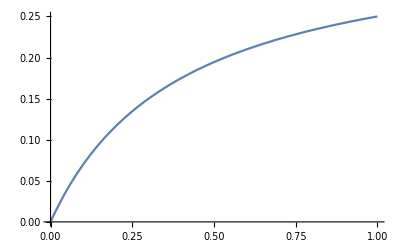

```mathematica
FR = (F*P)/(G+P)/.{G->0.4,F->0.35};
Plot[FR,{P,0,1}]
```

```mathematica
Csol = DSolve[CC'[t]==-(NN*s*F*CC[t])/(G + CC[t]/(Cmax*M)),CC[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{CC[t]→Cmax G M ProductLog[ⅇ^(-(F NN s t)/G+C[1]/(Cmax G M))/(Cmax G M)]}}

```mathematica
timetoextinction=Solve[ϵ*Cmax==CC[t]/.Csol[[1]],t]/.C[1]->Cstart
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→(Cstart-Cmax G M Log[Cmax ⅇ^(ϵ/(G M)) ϵ])/(Cmax F M NN s)}}

```mathematica
t/.timetoextinction[[1]]
```

(C[1]-Cmax G M Log[Cmax ⅇ^(ϵ/(G M)) ϵ])/(Cmax F M NN s)

Individuals harvested per meter^2 per second

```mathematica
harvestedtoextinction = ((1/M)*(Cmax-ϵ*Cmax))/(t/.timetoextinction[[1]])
```

(Cmax F NN s (Cmax-Cmax ϵ))/(C[1]-Cmax G M Log[Cmax ⅇ^(ϵ/(G M)) ϵ])

Individuals harvested per meter^2 per year

```mathematica
annualharvest=harvestedtoextinction*(60*60*24*365)*A
```

(31536000 A Cmax F NN s (Cmax-Cmax ϵ))/(C[1]-Cmax G M Log[Cmax ⅇ^(ϵ/(G M)) ϵ])

Individuals harvested per year in area the size of California

```mathematica
annualharvestCA = {(t/.timetoextinction[[1]])*(1/(60*60*24*365)),annualharvest}/.{M->2.5*10^6,Cmax->1.875*10^-6,G->0.4,NN->1,s->7.884*10^-8,F->0.35,C[1]->1.875*10^-6,ϵ->0.01,A->4.24*10^11}
```

{8.17834,0.0384944}

```mathematica
(1/M)*(Cmax-ϵ*Cmax)*A/.{M->2.5*10^6,Cmax->1.875*10^-6,ϵ->0.01,A->4.24*10^11}
```

0.31482